#### Basic Introduction

```mathematica
(* A comment is enclosed in bracket star - star bracket, which means this a comment *)
```

General usage :
Content is arranged in "cells", which are enclosed by a square bracket on the right. One can group cells by giving them a title. This is done by  selecting the bracket of the cell, and press Alt + 1 up to Alt + 7 to make it a title. Everything following that title will belong to that group until a new title comes. 
Clicking on the right - most bracket wil close or open the whole group.
   
To make a new line in a cell, press "enter"

To evaluate a cell just press "shift + enter" when you are somewhere in the cell
Input that is blue has not been evaluated, thus Mathematica knows nothing about it!

A semicolon after an expression suppresses the output.
  
Pure lazyness : % refers to the last result

Mathematica commands start with an uppercase letter, thus your own variables should start with lowercase to avoid problems.

#### Example differential equation solving

```mathematica
(*  First, we define some arbitrary starting values *)
A=0.1;
B=1;

(* Now, define the differential equations. Note that {...} just encloses a set, and one has to use a double "=" sign to define an equation to be solved *)

eqs={P1'[t]==-B P1[t]+(A+B) P2[t],
	P2'[t]== B P1[t]-(A+B) P2[t],
	P1[0]==1, 
	P2[0]==0};

(* Here, I define the analytic solutios of the rate equations, for comparison later on *)
P10=1; P20=0;
AnalyticP1[t_]=P10-1/(A+2 B)(1-ⅇ^(-(A+2 B)t)) (B P10-(A+B) P20);
AnalyticP2[t_]=P20+1/(A+2 B)(1-ⅇ^(-(A+2 B)t)) (B P10-(A+B) P20);
```

```mathematica
(* Now, numerically solve the equation. Mathematica does not give the solution. *)
solution=NDSolve[eqs,{P1,P2},{t,0,10}]
```

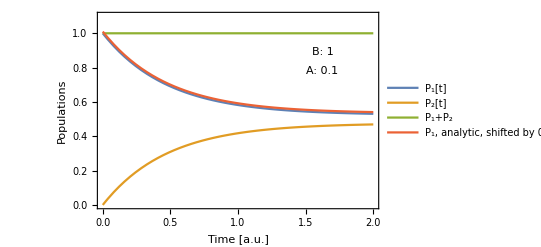

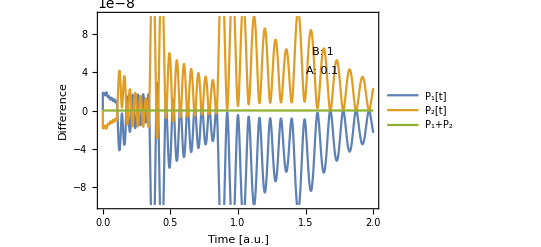

```mathematica
(* Take the solution and plug it into a function finally. The "/." command tells mathematica to replace P1 with the solution for P1 that we found. 
Thus the next command tells Mathematica to plot everything, P1, P2 and P1+P2, and replace P1, P2 with the solution we just found. We also plot the analytic expression for P1, shifted by 0.1 to make it visible. *)
Plot[Evaluate[{P1[t],P2[t],P1[t]+P2[t],AnalyticP1[t]+0.01}/.solution],{t,0,2},PlotRange->{All,{0,1.1}},
Frame->True,FrameLabel->{"Time [a.u.]","Populations"},
PlotLegends->{"P_1[t]","P_2[t]","P_1+P_2","P_1, analytic, shifted by 0.01"}, 
Epilog->{Text["A: "<>  ToString[A],Scaled[{0.8,0.7}]],Text["B: "<>  ToString[B],Scaled[{0.8,0.8}]]}]

(* To see how good the numerics works, plot the difference between analytic and numerical solution *)

Plot[Evaluate[{P1[t]-AnalyticP1[t],P2[t]-AnalyticP2[t],1-P1[t]-P2[t]}/.solution],{t,0,2},
Frame->True,FrameLabel->{"Time [a.u.]","Difference"},
PlotLegends->{"P_1[t]","P_2[t]","P_1+P_2"},
Epilog->{Text["A: "<>  ToString[A],Scaled[{0.8,0.7}]],Text["B: "<>  ToString[B],Scaled[{0.8,0.8}]]}]
```